{{-1.,0.367879},{-0.8,0.449329},{-0.6,0.548812},{-0.4,0.67032},{-0.2,0.818731},{0.,1.},{0.2,1.2214},{0.4,1.49182},{0.6,1.82212},{0.8,2.22554},{1.,2.71828}}

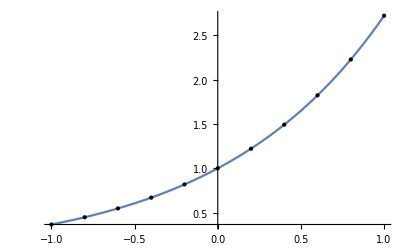

```mathematica
data=Table[{t,Exp[t]},{t,-1,1,0.2}];
Print[data]
degree=5;
basis = Table[ChebyshevT[k,t],{k,0,degree}];
fit = Fit[data,basis,t];
Plot[fit,{t,-1,1},Epilog->Point[data]]
```